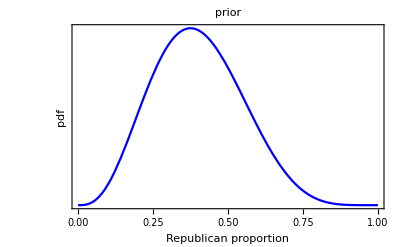

```mathematica
gPrior=Plot[PDF[BetaDistribution[4,6],x],{x,0,1},PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"Republican proportion","pdf"},BaseStyle->{FontSize->14},FrameTicks->{True,False},PlotLabel->"prior"]
```

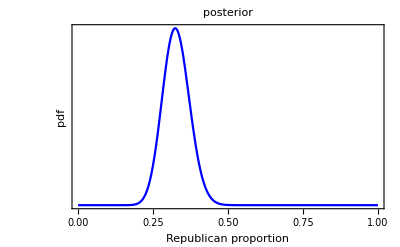

```mathematica
gPosterior=Plot[PDF[BetaDistribution[4+32,6+100-32],x],{x,0,1},PlotRange->Full,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"Republican proportion","pdf"},BaseStyle->{FontSize->14},FrameTicks->{True,False},PlotLabel->"posterior"]
```

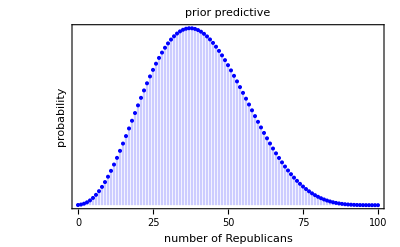

```mathematica
gPriorPredictive = DiscretePlot[PDF[BetaBinomialDistribution[4,6,100],x],{x,0,100},Frame->{True,True,False,False},FrameLabel->{"number of Republicans","probability"},BaseStyle->{FontSize->14},FrameTicks->{True,False},PlotStyle->Blue,PlotLabel->"prior predictive"]
```

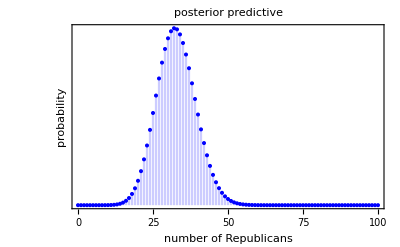

```mathematica
gPosteriorPredictive=DiscretePlot[PDF[BetaBinomialDistribution[4+32,6+100-32,100],x],{x,0,100},Frame->{True,True,False,False},FrameLabel->{"number of Republicans","probability"},BaseStyle->{FontSize->14},FrameTicks->{True,False},PlotStyle->Blue,PlotLabel->"posterior predictive"]
```

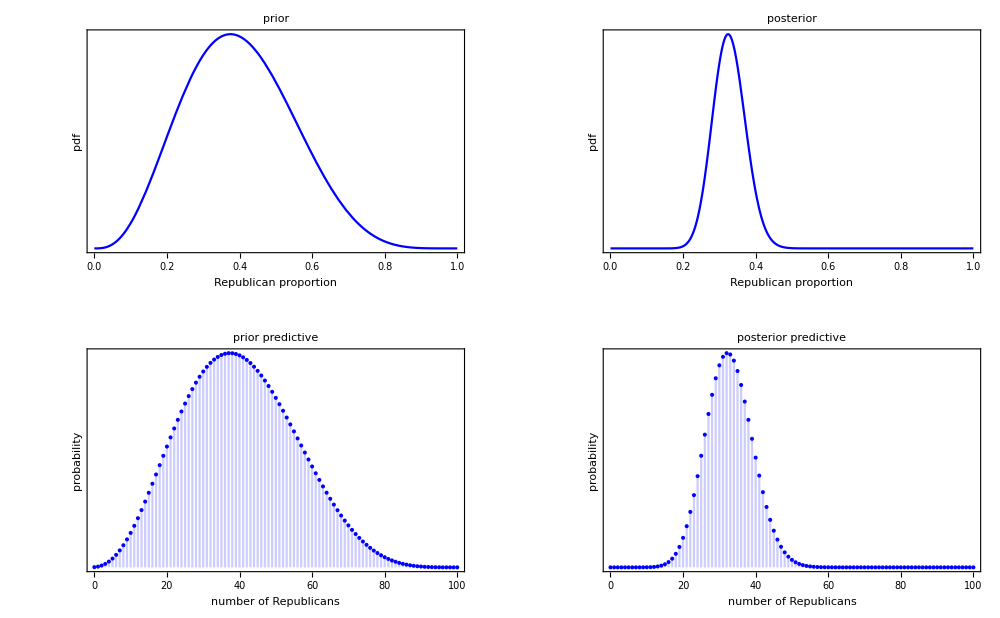

```mathematica
gFinal=Show[GraphicsGrid[{{gPrior,gPosterior},{gPriorPredictive,gPosteriorPredictive}}],ImageSize->1000]
```

```mathematica
Export["Posterior_priorPosteriorPredictiveVoting.pdf",gFinal]
```

Posterior_priorPosteriorPredictiveVoting.pdf

```mathematica
Maximize[{PDF[BetaBinomialDistribution[4+32,6+100-32,100],x],0≤ x ≤ 100},x,Integers]
```

{1226216740461633289494499961475/19966635712367686040991831631924,{x→32}}